```mathematica
8
```

# Simple Spectral Models and OLR

## Reproducing Nadir’s Simple Spectral Model

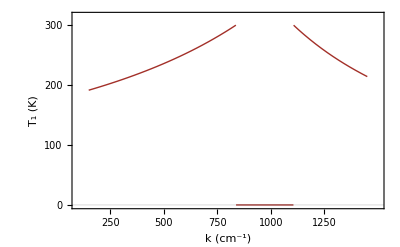

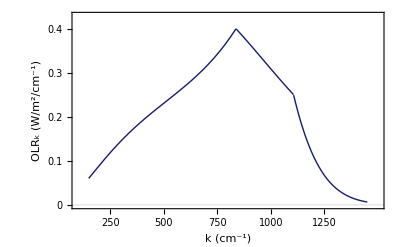

```mathematica
(* I will reproduce Figure B9 of Jeevanjee & Fueglistaler (2019b) *)

(* Constants (All given in SI Units)*)
σ = 5.67*10^-8;
h =6.63*10^-34;
kb = 1.38*10^-23;
c = 3*10^8;
Rd= 287.058;
Rv = 461.52; 
g= 9.81; 
Γ= 7/1000; 
L = 2260000; 
d = 1.50;
Tsurf=300;
Tstrat=200;
Tav=(Tsurf+Tstrat)/2;
RH=0.75;
Pref=101325 ;
Ps=Pref;
Pvinf=2.5*10^11;
krot=150*100; 
kvr=1450*100; 
κrot=260; 
κvr=10; 
lrot=60*100;
lvr=42*100;
hbar = h/(2*π);
WVP0 = d*Tav*RH*Pvinf/(Γ*L);

(* Functions (Note that k refers to the wave number, not the angular wavenumber as is common in the physics community.) *)
κ[k_]:=Piecewise[{{κrot*Exp[-(k-krot)/lrot],krot<=k<=1000*100},{κvr*Exp[-(kvr-k)/lvr],1000*100<k<=kvr}}];
τ0[k_]:=WVP0*κ[k]*Ps/Pref;
Tstar = Rd*Γ*L/(g*Rv);
T1[k_]:=Tstar/ProductLog[Tstar/Tsurf * τ0[k]^(Rd*Γ/g)];
t1[k_]:=Piecewise[{{T1[k],krot<k<k1rot[Tsurf]},{T1[k],k1vr[Tsurf]<k<kvr}}];
k1rot[T_]:=krot + lrot*(Log[κrot*WVP0]-L/(Rv*T));
k1vr[T_]:=kvr - lvr*(Log[κvr*WVP0]-L/(Rv*T));
Bν[k_]:=Piecewise[{{2*h*c^2*k^3/((Exp[h*c*k/(kb*Tsurf)]-1)),k1rot[Tsurf]<k<k1vr[Tsurf]},{2*h*c^2*k^3/((Exp[h*c*k/(kb*t1[k])]-1)),krot<k<k1rot[Tsurf]},{2*h*c^2*k^3/((Exp[h*c*k/(kb*t1[k])]-1)),k1vr[Tsurf]<k<kvr}}]

(* Plotting Functionality *)
(*arguments:min and max axis value,scale factor for tick length*)GetScaledLinearTicks[min_,max_,scale_]:=Module[{ticks},ticks=#[min,max]&/@{Charting`ScaledTicks[{Identity,Identity}],Charting`ScaledFrameTicks[{Identity,Identity}]};
(*scale the tick length*)Table[{#[[1]],#[[2]],scale*#[[3]]}&/@ticks[[i]],{i,2}]]

tticks={GetScaledLinearTicks[0,300,2.5],GetScaledLinearTicks[krot/100,kvr/100,2.5]};
bticks ={GetScaledLinearTicks[0,0.4,2.5],GetScaledLinearTicks[krot/100,kvr/100,2.5]};

(* Results *)
Plot[t1[100*k],{k,krot/100,kvr/100},PlotTheme->{"Scientific"},FrameLabel->{"k (cm^-1)",StringForm["`` (K)",Subscript[T,1]]},PlotStyle->{RGBColor[0.64,0.19,0.16],Thick},FrameStyle->Thickness[.003],FrameTicksStyle->Thickness[.0025],FrameTicks->tticks,PlotRange->{{krot/100-50,kvr/100+50},{0,315}}]

Plot[π*100*Bν[100*k],{k,krot/100,kvr/100},PlotTheme->{"Scientific"},FrameLabel->{"k (cm^-1)",StringForm["`` (W/m^2/cm^-1)",Subscript["OLR",k]]},PlotStyle->{RGBColor[23/255,29/255,108/255],Thick},FrameStyle->Thickness[.003],FrameTicksStyle->Thickness[.0025],FrameTicks->bticks,PlotRange->{{krot/100-50,kvr/100+50},{0,0.43}}]
```

## Showing the Window Closing at Higher Temperatures

```mathematica
(* Redefine these functions so Tsurf no longer equals 300K *)
T1[k_,Ts_]:=Tstar/ProductLog[Tstar/Ts* τ0[k]^(Rd*Γ/g)];
t1[k_,Ts_]=Piecewise[{{T1[k,Ts],krot<k<k1rot[Ts]},{T1[k,Ts],k1vr[Ts]<k<kvr}}];
Tem=Table[Table[{k,t1[100*k,Ts]},{k,krot/100+1,kvr/100-1,10}],{Ts,220,300,20}];

ListLinePlot[Tem,PlotTheme->{"Scientific"},PlotLabels->Table[Style[StringForm["T_s = ``K",Ts],Hue[Ts/300,1,.75]],{Ts,220,300,20}],FrameLabel->{"k (cm^-1)",StringForm["`` (K)",Subscript["T",1]]},FrameStyle->Thickness[.003],FrameTicksStyle->Thickness[.0025],FrameTicks->tticks,PlotRange->{{krot/100-50,kvr/100+50},{150,305}},PlotStyle->Table[Hue[Ts/300,1,.75],{Ts,220,300,20}]]
```

## Show the T_s Decoupling of OLR

```mathematica
(* I will reproduce the top part of Figure 3 of Koll & Cronin (2018) *)
Clear[Bν]
Bk[k_,Ts_]:=Piecewise[{{2*h*c^2*k^3/((Exp[h*c*k/(kb*Ts)]-1)),k1rot[Ts]<k<k1vr[Ts]},{2*h*c^2*k^3/((Exp[h*c*k/(kb*t1[k,Ts])]-1)),krot<k<k1rot[Ts]},{2*h*c^2*k^3/((Exp[h*c*k/(kb*t1[k,Ts])]-1)),k1vr[Ts]<k<kvr}}]
Bklist=Table[Table[{k,100*π*Bk[100*k,Ts]},{k,krot/100,kvr/100,10}],{Ts,220,300,20}];

bticks ={GetScaledLinearTicks[0,0.4,2.5],GetScaledLinearTicks[krot/100,kvr/100,2.5]};

ListLinePlot[Bklist,PlotTheme->{"Scientific"},PlotLabels->Table[Style[StringForm["``K",Ts],Hue[Ts/300,1,.75]],{Ts,220,300,20}],FrameLabel->{"k (cm^-1)",StringForm["`` (W/m^2/cm^-1)",Subscript["OLR",k]]},FrameStyle->Thickness[.003],FrameTicksStyle->Thickness[.0025],PlotStyle->Table[Hue[Ts/300,1,.75],{Ts,220,300,20}],FrameTicks->bticks,PlotRange-> Full, PlotRange->{{krot/100-50,kvr/100+50},{0,0.42}}]
```

-Graphics-

## Reproducing the Linearity of OLR

```mathematica
(* I will reproduce Figure 1 of Koll & Cronin (2018) *)

OLRk[k_]:=Table[π*Piecewise[{{2*h*c^2*k^3/((Exp[h*c*k/(kb*Ts)]-1)),k1rot[Ts]<k<k1vr[Ts]},{2*h*c^2*k^3/((Exp[h*c*k/(kb*t1[k,Ts])]-1)),krot<k<k1rot[Ts]},{2*h*c^2*k^3/((Exp[h*c*k/(kb*t1[k,Ts])]-1)),k1vr[Ts]<k<kvr}}],{Ts,220,300,2}];
OLR=Integrate[OLRk[k],{k,krot,kvr}]//N;
Tslist = Table[Ts,{Ts,220,300,2}];
OLRlist=Transpose[{Tslist,OLR}];
```

```mathematica
blackbody = Table[{Ts,σ*Ts^4},{Ts,200,304,1}];
bticks ={GetScaledLinearTicks[0,500,2.5],GetScaledLinearTicks[200,310,2.5]};

ListPlot[{OLRlist,blackbody},PlotTheme->{"Scientific"},FrameLabel->{"Near-surface Temperature (K)","Clearsky OLR (W/m^2)"},PlotStyle->{{RGBColor[23/255,29/255,108/255],PointSize[.011]},{RGBColor[0.64,0.19,0.16],PointSize[.011]}},FrameStyle->Thickness[.003],FrameTicksStyle->Thickness[.0025],FrameTicks->bticks,PlotRange->{{200,310},{0,500}},PlotLabels->{"Linear",StringForm["(σ``)^4",Subscript[T,s]]}]
```

-Graphics-

## Show Linearity of OLR Feedback with Simple Model

```mathematica
(* Derive λ = dOLR/dTs analytically and show that it depends on the width of the window region. *)
```